```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
```

This was the input, to use formulas to generate the vector labels

How to save this graphic as an image file:  Clicking on the graphic seems to allow editing it.  Click on the sidebar for the cell containing it, then File->Save Selection As

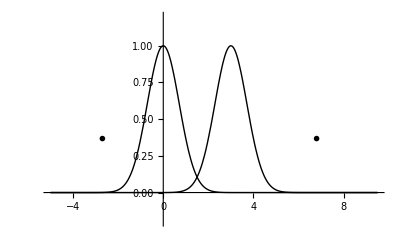

```mathematica
ClearAll[f, p, qmTwoL11fig2]
f[x_] := E^(- x^2)
p[r_] := With[{s = 1.9},Plot[{f[x], f[x -3]}, {x,-r, s r }, 
PlotStyle-> {{Thick, Black}, {Thick, Black}},
Ticks -> None,
PlotRange->{{-r, s r }, {-0.2, 1.2}}
]]
qmTwoL11fig2 = Show[{p[5], Graphics[{
Text[MaTeX["\\psi(x) = e^{-x^2}"], {-2.7, f[1]} ],
Text[MaTeX["\\psi'(x) = \\psi(x - a)"], {6.8, f[1]} ]
}]}]
(*Manipulate[ p[r], {r,  1, 30}]*)
```

```mathematica
E^(-x^2)
```

ⅇ^(-x^2)

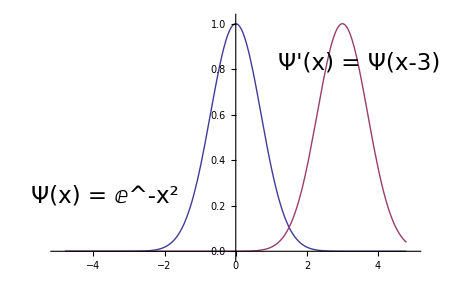

```mathematica
peeters`exportForLatex["qmTwoL11fig2", qmTwoL11fig2]
```

{qmTwoL11fig2.eps,qmTwoL11fig2pn.png}